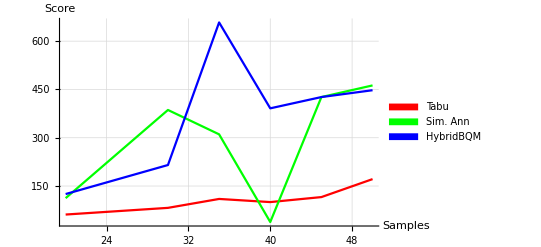

```mathematica
(*Motif Data FirstForm Clustering*)

motifTabuIner={{20,61.42},{30,82.17},{35,109.86},{40,100.12},{45, 115.65},{50,171.48}};
motifTabuSil={{20,0.31},{30,0.53},{35,0.55},{40, 0.55},{45, 0.38},{50,0.45}};
motifTabuHom={{20,0.31},{30,0.23},{35,0.21},{40,0.19},{45, 0.14},{50,0.17}};
motifTabuCom={{20,1.0},{30,1.0},{35,0.99},{40,1.0},{45, 0.94},{50,0.95}};
motifTabuVm={{20,0.47},{30,0.38},{35,0.35},{40, 0.32},{45, 0.25},{50,0.29}};

motifSimIner={{20,112.31},{30,386.25},{35,310.56},{40,38.21},{45, 426.36},{50,462.51}};
motifSimSil={{20,0.014},{30,-0.04},{35,-0.05},{40,-0.06},{45,-0.06},{50,-0.06}};
motifSimHom={{20, 0.31},{30,0.30},{35,0.22},{40, 0.25},{45,0.26},{50,0.26}};
motifSimCom={{20,0.86},{30,0.95},{35,0.88},{40, 0.83},{45,0.88},{50,0.92}};
motifSimVm={{20,0.45},{30,0.46},{35,0.44},{40, 0.39},{45,0.40},{50,0.41}};

motifHybridIner={{20,125.07},{30,215.25},{35,658.14},{40,391.33},{45,426.36},{50,447.62}};
motifHybridSil={{20,-0.11},{30,-0.12},{35,-0.02},{40,-0.05},{45,-0.06},{50, -0.07}};
motifHybridHom={{20, 0.32},{30,0.25},{35,0.28},{40,0.26},{45,0.27},{50, 0.25}};
motifHybridCom={{20,0.87},{30,0.90},{35,0.92},{40,0.86},{45,0.91},{50,0.89}};
motifHybridVm={{20,0.47},{30,0.39},{35,0.43},{40,0.40},{45,0.42},{50,0.39}};


(*Motif Kmeans*)

motifDefInerKm={{20,21.36},{30,24.54},{35,28.19},{40,34.16},{45,38.85},{50,44.38}};
motifDefSilKm={{20,0.37},{30,0.51},{35, 0.52},{40,0.52},{45,0.52},{50,0.50}};
motifDefHomKm={{20,0.37},{30,0.27},{35,0.24},{40,0.22},{45,0.21},{50,0.21}};
motifDefComKm={{20,1.0},{30,1.0},{35,0.99},{40,0.99},{45,0.99},{50,1.0}};
motifDefVmKm={{20,0.54},{30,0.42},{35,0.39},{40,0.36},{45,0.35},{50,0.36}};
motifDefIterKm = { {20, 5}, {30,6 }, {35, 4}, {40, 2}, {45, 8}, {50, 4} };

motifTabuInerKm={{20,18.47},{30,25.57},{35,28.79},{40,34.71},{45,39.00},{50,44.46}};
motifTabuSilKm={{20,0.44},{30,0.52},{35,0.55},{40,0.54},{45,0.53},{50,0.50}};
motifTabuHomKm={{20,0.34},{30,0.23},{35,0.21},{40,0.19},{45,0.20},{50,0.20}};
motifTabuComKm={{20,1.0},{30,0.94},{35,0.99},{40,0.95},{45,0.95},{50,0.96}};
motifTabuVmKm={{20,0.51},{30,0.37},{35,0.35},{40,0.32},{45,0.33},{50,0.34}};
motifTabuIterKm = { {20, 4}, {30, 5}, {35, 4}, {40, 4}, {45, 4}, {50, 5} };

motifSimInerKm={{20,21.36},{30,24.54},{35,28.19},{40,85.69},{45,100.76},{50,44.38}};
motifSimSilKm={{20,0.37},{30,0.51},{35,0.52},{40,0.45},{45,0.45},{50,0.50}};
motifSimHomKm={{20,0.37},{30,0.27},{35,0.24},{40,0.06},{45,0.05},{50,0.21}};
motifSimComKm={{20,1.0},{30,1.0},{35,0.99},{40,0.99},{45,1.0},{50,1.0}};
motifSimVmKm={{20,0.54},{30,0.42},{35,0.39},{40,0.12},{45,0.11},{50,0.36}};
motifSimIterKm = { {20,3 }, {30, 4}, {35, 6}, {40,2 }, {45,2 }, {50,8} };

motifHybridInerKm={{20,21.44},{30,24.54},{35,74.46},{40,34.24},{45,100.76},{50,50.27}};
motifHybridSilKm={{20,0.35},{30,0.51},{35,0.45},{40,0.52},{45,0.45},{50,0.39}};
motifHybridHomKm={{20,0.38},{30,0.27},{35,0.07},{40,0.20},{45,0.05},{50,0.28}};
motifHybridComKm={{20,0.99},{30,1.0},{35,0.99},{40,0.95},{45,1.0},{50,0.99}};
motifHybridVmKm={{20,0.55},{30,0.42},{35,0.13},{40,0.34},{45,0.11},{50,0.44}};
motifHybridIterKm = { {20, 5}, {30, 3}, {35, 2}, {40, 3}, {45, 2}, {50,5 } };


(* Inertia Plots no kmeans *)

motifTabuInerPlot = ListLinePlot[motifTabuIner, PlotStyle->{Red}];
motifSimInerPlot = ListLinePlot[motifSimIner, PlotStyle->{Green}];
motifHybridInerPlot = ListLinePlot[motifHybridIner, PlotStyle->{Blue}];
motifDefInerPlotKm = ListLinePlot[motifDefInerKm, PlotStyle ->{Red}];
motifTabuInerPlotKm = ListLinePlot[motifTabuInerKm, PlotStyle->{Green}];
motifSimInerPlotKm = ListLinePlot[motifSimInerKm, PlotStyle->{Blue}];
motifHybridInerPlotKm = ListLinePlot[motifHybridIner, PlotStyle->{Black}];

Legended[
Show[motifTabuInerPlot,motifSimInerPlot, motifHybridInerPlot,
AxesLabel->{"Samples", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[ {Red, Green, Blue}, 
{"Tabu", "Sim. Ann", "HybridBQM"} ]
]
```

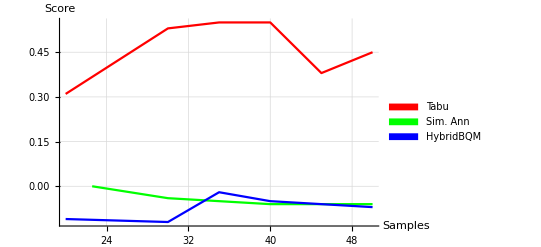

```mathematica
(* Silhouette Plots no kmeans *)

motifTabuSilPlot=ListLinePlot[motifTabuSil,PlotStyle->{Red}];
motifSimSilPlot=ListLinePlot[motifSimSil,PlotStyle->{Green}];
motifHybridSilPlot=ListLinePlot[motifHybridSil,PlotStyle->{Blue}];
motifDefSilPlotKm=ListLinePlot[motifDefSilKm,PlotStyle->{Red}];
motifTabuSilPlotKm=ListLinePlot[motifTabuSilKm,PlotStyle->{Green}];
motifSimSilPlotKm=ListLinePlot[motifSimSilKm,PlotStyle->{Blue}];
motifHybridSilPlotKm=ListLinePlot[motifHybridSil,PlotStyle->{Black}];

Legended[Show[motifTabuSilPlot,motifSimSilPlot,motifHybridSilPlot,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue},{"Tabu","Sim. Ann","HybridBQM"}]]
```

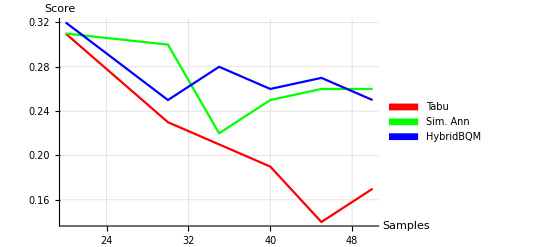

```mathematica
motifTabuHomPlot=ListLinePlot[motifTabuHom,PlotStyle->{Red}];
motifSimHomPlot=ListLinePlot[motifSimHom,PlotStyle->{Green}];
motifHybridHomPlot=ListLinePlot[motifHybridHom,PlotStyle->{Blue}];
motifDefHomPlotKm=ListLinePlot[motifDefHomKm,PlotStyle->{Red}];
motifTabuHomPlotKm=ListLinePlot[motifTabuHomKm,PlotStyle->{Green}];
motifSimHomPlotKm=ListLinePlot[motifSimHomKm,PlotStyle->{Blue}];
motifHybridHomPlotKm=ListLinePlot[motifHybridHom,PlotStyle->{Black}];

Legended[Show[motifTabuHomPlot,motifSimHomPlot,motifHybridHomPlot,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue},{"Tabu","Sim. Ann","HybridBQM"}]]
```

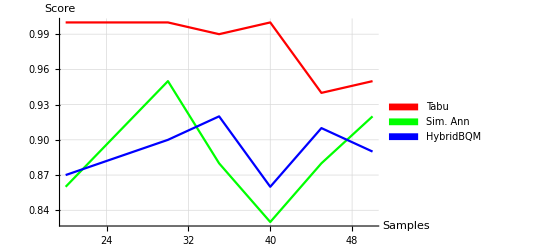

```mathematica
(* Completness *) 

motifTabuComPlot=ListLinePlot[motifTabuCom,PlotStyle->{Red}];
motifSimComPlot=ListLinePlot[motifSimCom,PlotStyle->{Green}];
motifHybridComPlot=ListLinePlot[motifHybridCom,PlotStyle->{Blue}];
motifDefComPlotKm=ListLinePlot[motifDefComKm,PlotStyle->{Red}];
motifTabuComPlotKm=ListLinePlot[motifTabuComKm,PlotStyle->{Green}];
motifSimComPlotKm=ListLinePlot[motifSimComKm,PlotStyle->{Blue}];
motifHybridComPlotKm=ListLinePlot[motifHybridCom,PlotStyle->{Black}];

Legended[Show[motifTabuComPlot,motifSimComPlot,motifHybridComPlot,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue},{"Tabu","Sim. Ann","HybridBQM"}]]
```

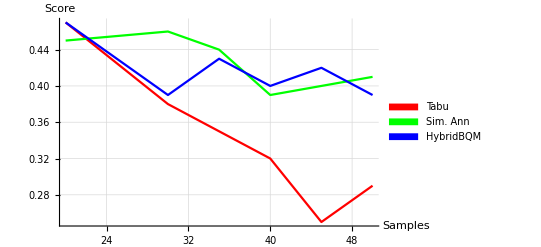

```mathematica
(* Vmeasure *)

motifTabuVmPlot=ListLinePlot[motifTabuVm,PlotStyle->{Red}];
motifSimVmPlot=ListLinePlot[motifSimVm,PlotStyle->{Green}];
motifHybridVmPlot=ListLinePlot[motifHybridVm,PlotStyle->{Blue}];
motifDefVmPlotKm=ListLinePlot[motifDefVmKm,PlotStyle->{Red}];
motifTabuVmPlotKm=ListLinePlot[motifTabuVmKm,PlotStyle->{Green}];
motifSimVmPlotKm=ListLinePlot[motifSimVmKm,PlotStyle->{Blue}];
motifHybridVmPlotKm=ListLinePlot[motifHybridVm,PlotStyle->{Black}];

Legended[Show[motifTabuVmPlot,motifSimVmPlot,motifHybridVmPlot,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue},{"Tabu","Sim. Ann","HybridBQM"}]]
```

```mathematica
(* Kmeans Plots *)
```

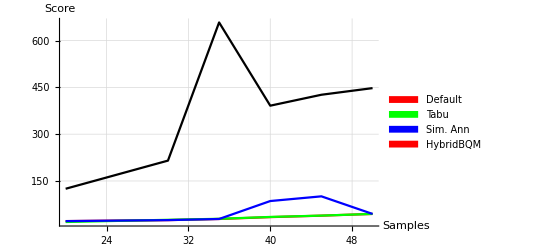

```mathematica
Legended[Show[motifDefInerPlotKm,motifTabuInerPlotKm,motifSimInerPlotKm,motifHybridInerPlotKm,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Red},{"Default","Tabu","Sim. Ann","HybridBQM"}]]
```

```mathematica
(* Silhouette *)
```

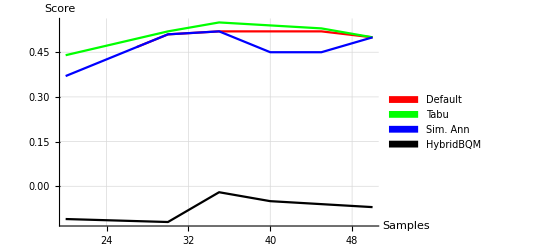

```mathematica
Legended[Show[motifDefSilPlotKm,motifTabuSilPlotKm,motifSimSilPlotKm,motifHybridSilPlotKm,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default","Tabu","Sim. Ann","HybridBQM"}]]
```

```mathematica
(* Homog *)
```

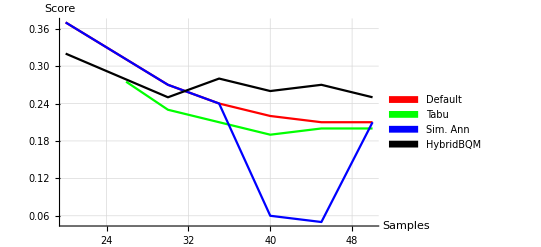

```mathematica
Legended[Show[motifDefHomPlotKm,motifTabuHomPlotKm,motifSimHomPlotKm,motifHybridHomPlotKm,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default","Tabu","Sim. Ann","HybridBQM"}]]
```

```mathematica
(* Completeness *)
```

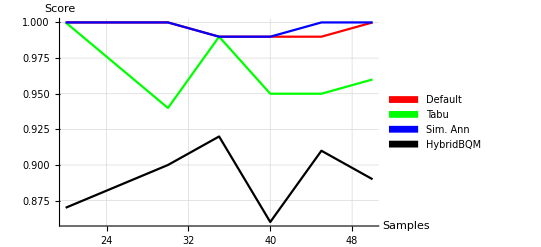

```mathematica
Legended[Show[motifDefComPlotKm,motifTabuComPlotKm,motifSimComPlotKm,motifHybridComPlotKm,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default","Tabu","Sim. Ann","HybridBQM"}]]
```

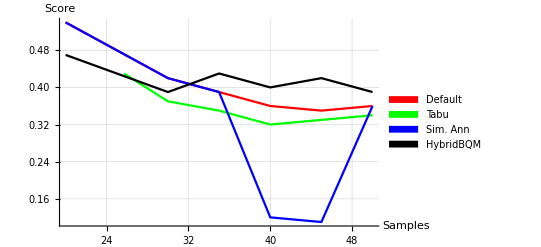

```mathematica
(* Vmeasure *)

Legended[Show[motifDefVmPlotKm,motifTabuVmPlotKm,motifSimVmPlotKm,motifHybridVmPlotKm,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default","Tabu","Sim. Ann","HybridBQM"}]]
```

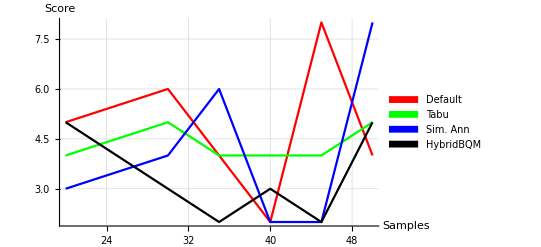

```mathematica
(* Iterations *)

motifDefIterPlotKm=ListLinePlot[motifDefIterKm,PlotStyle->{Red}];
motifTabuIterPlotKm=ListLinePlot[motifTabuIterKm,PlotStyle->{Green}];
motifSimIterPlotKm=ListLinePlot[motifSimIterKm,PlotStyle->{Blue}];
motifHybridIterPlotKm=ListLinePlot[motifHybridIterKm,PlotStyle->{Black}];


Legended[Show[motifDefIterPlotKm,motifTabuIterPlotKm,motifSimIterPlotKm,motifHybridIterPlotKm,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default","Tabu","Sim. Ann","HybridBQM"}]]
```